Name: Karan Sharma
College Roll No.: 2232191
University Roll No. : 22036563079
Class: BSc (Hons) Mathematics / Year 3 / Complex Analysis
Section: A

# PRACTICAL 3

(a) Write parametric equations and make a parametric plot for an ellipse centered at the origin with horizontal major axis of 4 units and vertical minor axis of 2 units. 
(b) Show the effect of rotation of this ellipse by an angle of π/6 radians and shifting of the centre from (0,0) to (2,1), by making a parametric plot.

```mathematica
(*To plot a parametric equations, we may use the ParametricPlot[] command*)
```

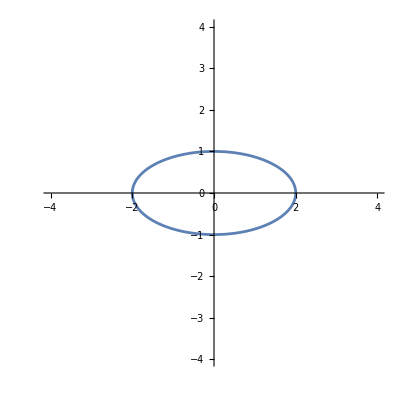

```mathematica
(*the equation of the ellipse is x^2/2^2+y^2/1=1*)
a=ParametricPlot[{2*Cos[t], Sin[t]},{t,0,2π},PlotRange->4]
```

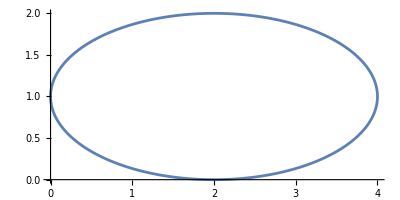

```mathematica
(*Translate the center to the point (2,1)*)
b=ParametricPlot[{2*Cos[t]+2, Sin[t]+1},{t,0,2π}]
```

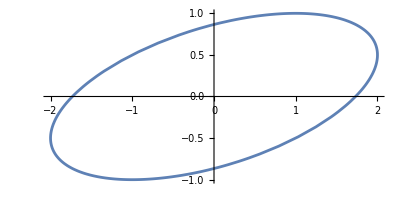

```mathematica
(*Rotate the ellipse about the origin by an angle of π/6*)
c=ParametricPlot[{2*Cos[t], Sin[t+π/6]},{t,0,2π}]
```

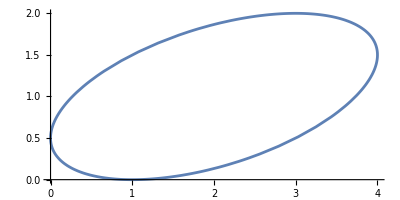

```mathematica
(*Rotate and translate*)
d=ParametricPlot[{2*Cos[t]+2, Sin[t+π/6]+1},{t,0,2π}]
```

Using ParametricPlot command

```mathematica
ClearAll;
```

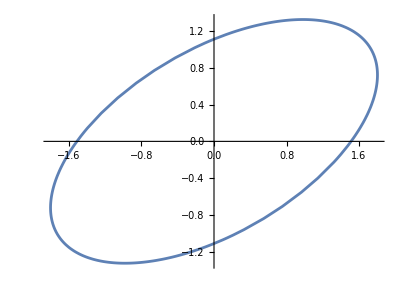

```mathematica
e=ParametricPlot[RotationTransform[π/6][{2*Cos[t], Sin[t]}],{t,0,2π}]
```

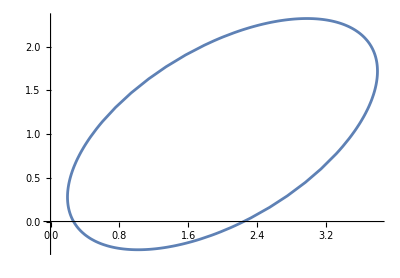

```mathematica
f=ParametricPlot[TranslationTransform[{2,1}][RotationTransform[π/6][{2*Cos[t], Sin[t]}]],{t,0,2π}]
```

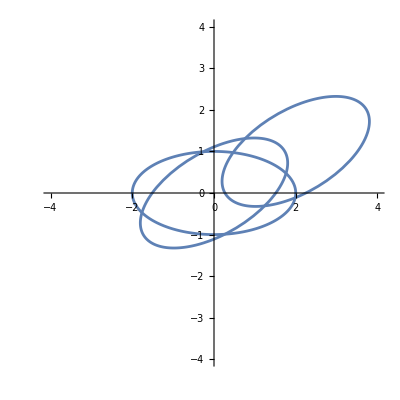

```mathematica
Show[a,e,f]
```

```mathematica
ClearAll;
a=ParametricPlot[
{{2Cos[t], Sin[t]},
RotationTransform[π/6][{2Cos[t], Sin[t]}],
TranslationTransform[{2,1}][RotationTransform[π/6][{2Cos[t], Sin[t]}]]},
{t,0,2π},PlotLegends->{"Ellipse", "Rotated Ellipse", "Rotated and Translated Ellipse",AxesLabel->{"Real Axis","Imaginary Axis"},PlotRange->4}
];
b=PolarPlot[2,{θ,0,2π},PolarGridLines->True,PlotStyle->Opacity[0],PolarAxes->True];
Show[a,b]
```

-Graphics-

```mathematica
Manipulate[
ParametricPlot[
{{2Cos[t], Sin[t]},
RotationTransform[π/6][{2Cos[t], Sin[t]}],
TranslationTransform[{2,1}][RotationTransform[τ][{2Cos[t], Sin[t]}]]},
{t,0,2π},PlotLegends->{"Ellipse", "Rotated Ellipse", "Rotated and Translated Ellipse"}
],{τ,0,2π}
]
```